```mathematica
NN = 2
```

2

```mathematica
m = 0.3 - ⅈ 0.4
```

0.3-0.4 ⅈ

```mathematica
cc[k_]  :=  Exp[ (ⅈ 2 π k)/NN]
circ= Array[cc, NN, 0];
```

```mathematica
mm = m circ
```

{0.3-0.4 ⅈ,-0.3+0.4 ⅈ}

```mathematica
σ[k_] := ( 1 + ( -m )^NN )^(1/NN) circ[[k]]
```

```mathematica
∏_(l=0)^(NN-1) ( σ[2]  +  mm[[l + 1]] )    -  1   // N
```

0.+5.78964×10^-17 ⅈ

```mathematica
Abs[σ[2]]
```

0.980035

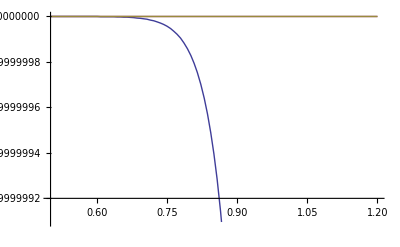

```mathematica
Plot[{ Abs[ (1 + ( - λ m)^21)^(1/21)],Abs[ (1 + ( - λ m)^51)^(1/51)],Abs[ (1 + ( - λ m)^101)^(1/101)]} , { λ, 0.5, 1.2}]
```

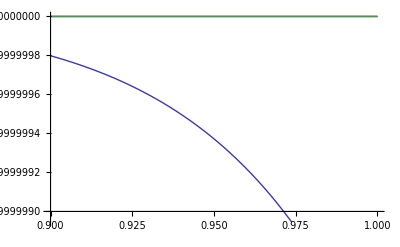

```mathematica
Plot[{ Abs[ (1 + ( - λ m)^21)^(1/21)],Abs[ (1 + ( - λ m)^51)^(1/51)],Abs[ (1 + ( - λ m)^101)^(1/101)],
          Abs[ (1 + ( - λ m)^201)^(1/201)]} , { λ, 0.9, 1.0}]
```

```mathematica
Ndepf[k_] := Abs[ (1 + ( - m)^k)^(1/k)]
```

```mathematica
Ndepfeven[k_] := Abs[ (1 + ( - m)^(2k))^(1/(2k))]
```

```mathematica
Ndepfodd[k_] := Abs[ (1 + ( - m)^(2k + 1))^(1/(2k + 1))]
```

```mathematica
Ndep =Array[Ndepf,100, 2];
```

```mathematica
Ndepeven = Array[Ndepfeven, 100, 1];
```

```mathematica
Ndepodd = Array[Ndepfodd, 100, 1];
```

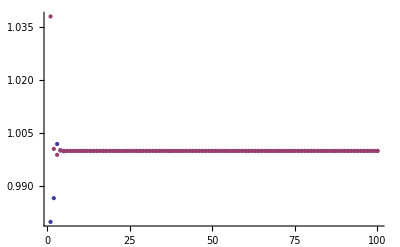

```mathematica
ListPlot[{Ndepeven, Ndepodd}]
```

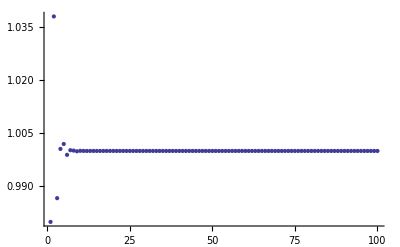

```mathematica
ListPlot[Ndep]
```